```mathematica
ClearAll["Global`*"]
```

## Nd150

```mathematica
enData1={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strData1={0.00006,0.00016,0.00040,0.00094,0.00212,0.00451,0.00906,0.01724,0.03103,0.05284,0.08511,0.12970,0.18699,0.25504,0.32911,0.40177,0.46403,0.50706,0.52428,0.51307,0.47555,0.41822,0.35059,0.28340,0.22701,0.19040,0.18084,0.20393,0.26358,0.36151,0.49633,0.66249,0.84959,1.04285,1.22474,1.37767,1.48703,1.54364,1.54485,1.49435,1.40065,1.27519,1.13069,0.97990,0.83505,0.70742,0.60678,0.54055,0.51263,0.52225,0.56337,0.62494,0.69235,0.74997,0.78420,0.78621,0.75364,0.69059,0.60599,0.51104,0.41643,0.33031,0.25741,0.19932,0.15552,0.12451,0.10483,0.09551,0.09613,0.10649,0.12626,0.15462,0.19018,0.23105,0.27518,0.32074,0.36638,0.41136,0.45534,0.49797,0.53830,0.57448,0.60358,0.62204,0.62645,0.61455,0.58602,0.54281,0.48879,0.42886,0.36788,0.30965,0.25654,0.20948,0.16842,0.13291,0.10250,0.07697,0.05625,0.04034,0.02915,0.02242,0.01975,0.02058,0.02421,0.02978,0.03630,0.04267,0.04782,0.05085,0.05122,0.04883,0.04405,0.03759,0.03035,0.02319,0.01676,0.01146,0.00741,0.00453,0.00263,0.00144,0.00075,0.00037,0.00017,0.00007,0.00003,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00003,0.00009,0.00027,0.00082,0.00232,0.00622,0.01579,0.03791,0.08611,0.18505,0.37622,0.72362,1.31675,2.26680,3.69181,5.68831,8.29173,11.43469,14.91836,18.41346,21.50143,23.75292,24.82471,24.54533,22.95997,20.31848,17.01096,13.47361,10.09617,7.15727,4.80015,3.04566,1.82820,1.03821,0.55778,0.28350,0.13632,0.06202,0.02669,0.01087,0.00419,0.00153,0.00053,0.00017,0.00005,0.00002};
enData2={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strData2={0.00008,0.00011,0.00014,0.00018,0.00021,0.00023,0.00025,0.00025,0.00024,0.00023,0.00021,0.00020,0.00019,0.00019,0.00019,0.00021,0.00022,0.00023,0.00023,0.00022,0.00021,0.00019,0.00017,0.00016,0.00015,0.00014,0.00014,0.00014,0.00015,0.00016,0.00017,0.00018,0.00019,0.00021,0.00022,0.00024,0.00025,0.00026,0.00026,0.00026,0.00026,0.00025,0.00024,0.00023,0.00023,0.00022,0.00022,0.00023,0.00023,0.00024,0.00024,0.00025,0.00025,0.00026,0.00027,0.00027,0.00027,0.00026,0.00025,0.00023,0.00020,0.00017,0.00013,0.00011,0.00008,0.00006,0.00005,0.00004,0.00004,0.00004,0.00004,0.00004,0.00005,0.00006,0.00007,0.00007,0.00008,0.00009,0.00009,0.00009,0.00010,0.00009,0.00009,0.00008,0.00007,0.00006,0.00006,0.00005,0.00004,0.00004,0.00004,0.00003,0.00003,0.00003,0.00003,0.00002,0.00002,0.00001,0.00001,0.00001,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00001,0.00001,0.00002,0.00002,0.00003,0.00003,0.00004,0.00004,0.00004,0.00005,0.00005,0.00005,0.00005,0.00005,0.00004,0.00004,0.00003,0.00003,0.00002,0.00002,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00002,0.00002,0.00002,0.00002,0.00002,0.00002,0.00001,0.00001,0.00001,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00001,0.00001,0.00002,0.00004,0.00006,0.00008,0.00012,0.00017,0.00022,0.00028,0.00033,0.00037,0.00040,0.00041,0.00039,0.00035,0.00030,0.00025,0.00019,0.00014,0.00010,0.00006,0.00004,0.00002,0.00001,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000};
```

## Sm150

```mathematica
enData3={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strData3={0.00029,0.00054,0.00093,0.00152,0.00235,0.00347,0.00486,0.00650,0.00830,0.01016,0.01199,0.01371,0.01525,0.01659,0.01768,0.01848,0.01890,0.01886,0.01830,0.01721,0.01569,0.01395,0.01222,0.01077,0.00983,0.00954,0.00991,0.01091,0.01242,0.01432,0.01649,0.01888,0.02147,0.02431,0.02744,0.03092,0.03472,0.03872,0.04268,0.04624,0.04897,0.05045,0.05039,0.04868,0.04550,0.04128,0.03662,0.03218,0.02851,0.02600,0.02476,0.02465,0.02535,0.02646,0.02757,0.02840,0.02878,0.02868,0.02812,0.02718,0.02594,0.02443,0.02271,0.02085,0.01895,0.01712,0.01550,0.01417,0.01320,0.01256,0.01222,0.01210,0.01212,0.01223,0.01242,0.01268,0.01307,0.01361,0.01436,0.01533,0.01649,0.01776,0.01902,0.02011,0.02089,0.02123,0.02106,0.02040,0.01930,0.01790,0.01630,0.01465,0.01302,0.01149,0.01012,0.00895,0.00802,0.00737,0.00701,0.00695,0.00718,0.00767,0.00838,0.00925,0.01024,0.01129,0.01233,0.01329,0.01411,0.01473,0.01507,0.01512,0.01483,0.01422,0.01330,0.01213,0.01076,0.00927,0.00776,0.00631,0.00500,0.00390,0.00308,0.00255,0.00235,0.00247,0.00290,0.00360,0.00448,0.00544,0.00635,0.00710,0.00761,0.00782,0.00777,0.00753,0.00722,0.00692,0.00671,0.00658,0.00649,0.00637,0.00614,0.00574,0.00516,0.00444,0.00364,0.00283,0.00209,0.00147,0.00099,0.00065,0.00044,0.00035,0.00039,0.00055,0.00087,0.00138,0.00211,0.00308,0.00428,0.00565,0.00708,0.00845,0.00959,0.01035,0.01063,0.01039,0.00967,0.00857,0.00723,0.00580,0.00444,0.00323,0.00224,0.00149,0.00095,0.00061,0.00048,0.00061,0.00119,0.00270,0.00605,0.01296,0.02634,0.05065,0.09217,0.15867,0.25842,0.39818,0.58041,0.80041,1.04427,1.28892,1.50507,1.66268,1.73770,1.71814,1.60717,1.42227,1.19075,0.94314,0.70672,0.50100,0.33601,0.21319,0.12797,0.07267,0.03904,0.01984,0.00954,0.00434,0.00187,0.00076,0.00029,0.00011,0.00004,0.00001,0.00000,0.00000};
```

## Numerical params

```mathematica
elem[el_,n_]:=Style[Row[{Superscript["",n],StringTemplate["``"][el]}]];
xdp=1.45;
chi12=0.64;
el1=elem["Nd",150];
el2=elem["Sm",150];
```

## Figures

### Figure1

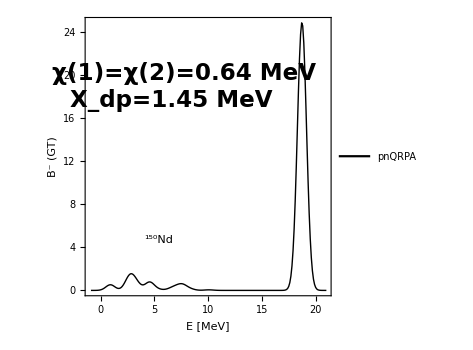

```mathematica
tableFig1=Table[{enData1[[i]],strData1[[i]]},{i,1,Length[strData1]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,21},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.4,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.2}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_8/new_figs/fig1_set8.pdf",Show[fig1],ImageResolution->1200];
```

### Figure2

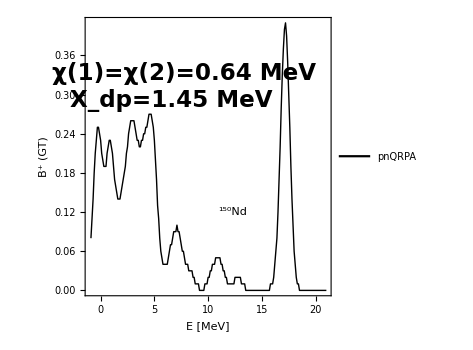

```mathematica
tableFig2=Table[{enData2[[i]],strData2[[i]]*1000},{i,1,Length[strData2]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,21},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.6,0.3}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_8/new_figs/fig2_set8.pdf",Show[fig2],ImageResolution->1200];
```

### Figure3

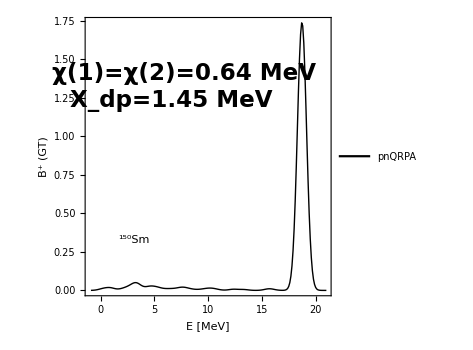

```mathematica
tableFig3=Table[{enData3[[i]],strData3[[i]]},{i,1,Length[strData3]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,21},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el2,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.2}]]}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_8/new_figs/fig3_set8.pdf",Show[fig3],ImageResolution->1200];
```